```mathematica
Clear[x]
rmin=-5
rmax=5
```

-5

5

ⅇ^(ⅈ √2 x)

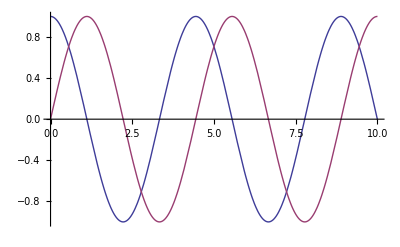

```mathematica
Amp0 = ManyAmp[0,1,1]
Plot[{Re[Amp0],Im[Amp0]},{x,0,10}]
```

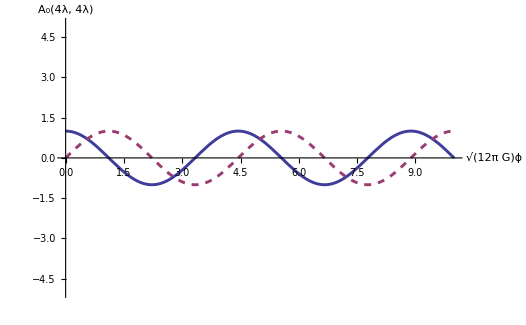

```mathematica
pre0 = Plot[{Re[Amp0],Im[Amp0]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_0(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

9/2 (-1/36 ⅇ^(ⅈ √2 x)+1/36 ⅇ^(2 ⅈ √2 x)-(ⅈ ⅇ^(ⅈ √2 x) x)/(12 √2))

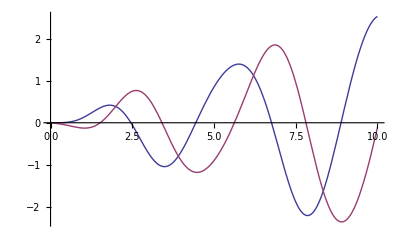

```mathematica
Amp2=ManyAmp[2,1,1]
Plot[{Re[Amp2],Im[Amp2]},{x,0,10}]
```

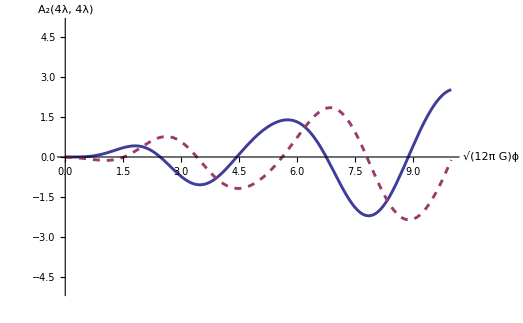

```mathematica
pre0 = Plot[{Re[Amp2],Im[Amp2]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_2(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

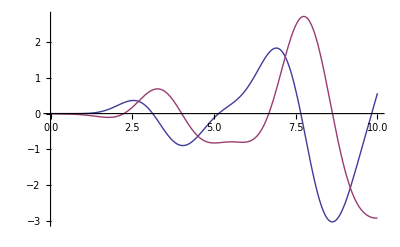

```mathematica
Amp4=ManyAmp[4,1,1];
Plot[{Re[Amp4],Im[Amp4]},{x,0,10}]
```

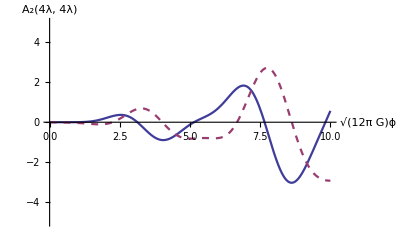

```mathematica
pre0 = Plot[{Re[Amp4],Im[Amp4]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_2(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

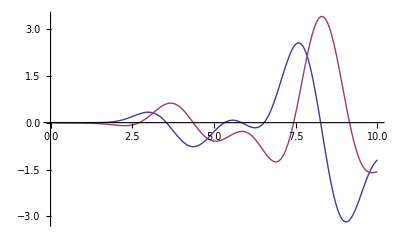

```mathematica
Amp6=ManyAmp[6,1,1];
Plot[{Re[Amp6],Im[Amp6]},{x,0,10}]
```

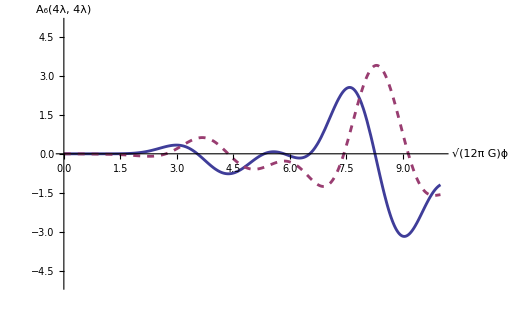

```mathematica
pre0 = Plot[{Re[Amp6],Im[Amp6]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_6(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

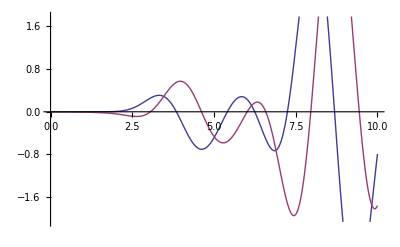

```mathematica
Amp8=ManyAmp[8,1,1];
Plot[{Re[Amp8],Im[Amp8]},{x,0,10}]
```

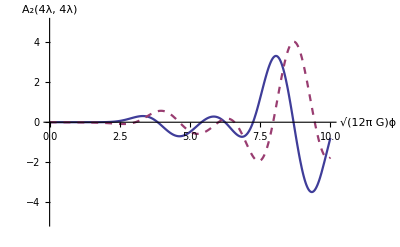

```mathematica
pre0 = Plot[{Re[Amp8],Im[Amp8]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_2(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

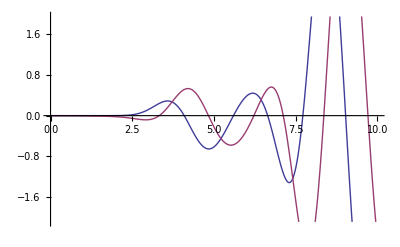

```mathematica
Amp10=ManyAmp[10,1,1];
Plot[{Re[Amp10],Im[Amp10]},{x,0,10}]
```

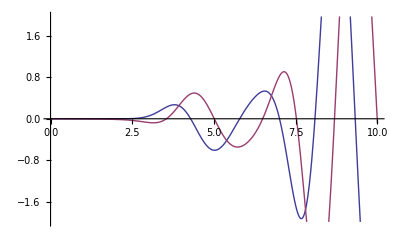

```mathematica
Amp12=ManyAmp[12,1,1];
Plot[{Re[Amp12],Im[Amp12]},{x,0,10}]
```

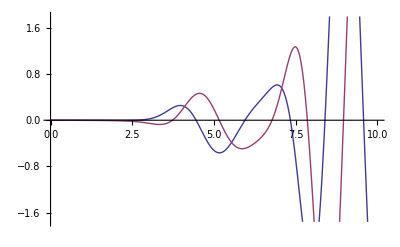

```mathematica
Amp14=ManyAmp[14,1,1];
Plot[{Re[Amp14],Im[Amp14]},{x,0,10}]
```

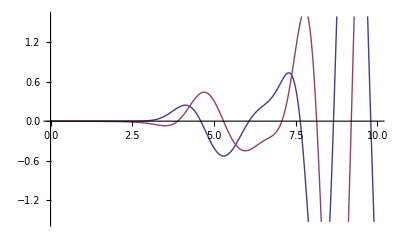

```mathematica
Amp16=ManyAmp[16,1,1];
Plot[{Re[Amp16],Im[Amp16]},{x,0,10}]
```

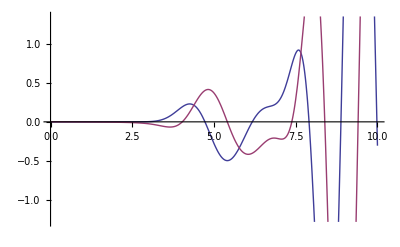

```mathematica
Amp18=ManyAmp[18,1,1];
Plot[{Re[Amp18],Im[Amp18]},{x,0,10}]
```

```mathematica
TotalAmp=Amp0+Amp2+Amp4+Amp6+Amp8+Amp10+Amp12+Amp14+Amp16+Amp18;
```

```mathematica
aex = Aexact[1,1];
```

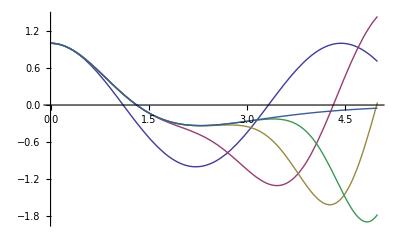

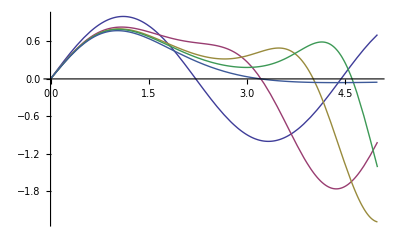

```mathematica
Plot[{Re[Amp0],Re[Amp0+Amp2+Amp4],Re[Amp0+Amp2+Amp4+Amp6+Amp8+Amp10],Re[TotalAmp],Re[aex]},{x,0,5}]
Plot[{Im[Amp0],Im[Amp0+Amp2+Amp4],Im[Amp0+Amp2+Amp4+Amp6+Amp8+Amp10],Im[TotalAmp],Im[aex]},{x,0,5}]
```

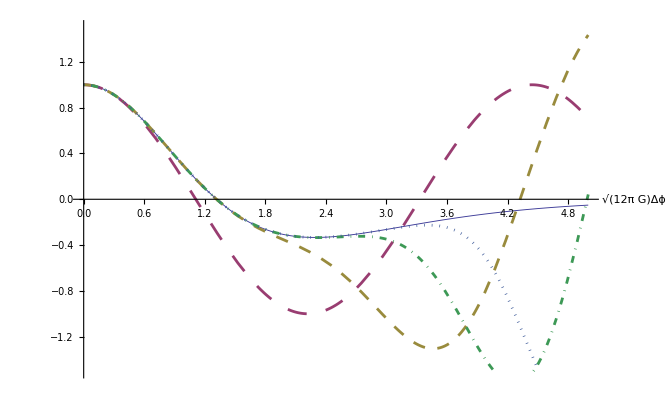

```mathematica
Plot[{Re[aex],Re[Amp0],Re[Amp0+Amp2+Amp4],Re[Amp0+Amp2+Amp4+Amp6+Amp8+Amp10],Re[TotalAmp]},{x,0,5},AxesLabel->{"√(12π G)Δϕ",},PlotRange->{-1.5,1.5},LabelStyle->Medium,PlotStyle->{{Thickness[0.001]}, {Thickness[0.003],Dashing[{Large}]},{Thickness[0.003],Dashing[Medium]},{Thickness[0.003],DotDashed},{Thickness[0.003],Dotted}}]
```

4.1

{{0.,0.884717-0.466128 ⅈ},{2.,-0.546673-1.00668 ⅈ},{4.,-0.890814-0.129537 ⅈ},{6.,-0.65674+0.355713 ⅈ},{8.,-0.309661+0.546108 ⅈ},{10.,-0.0127635+0.516286 ⅈ},{12.,0.164997+0.384552 ⅈ},{14.,0.237287+0.237748 ⅈ},{16.,0.241229+0.116637 ⅈ},{18.,0.210405+0.0322181 ⅈ}}

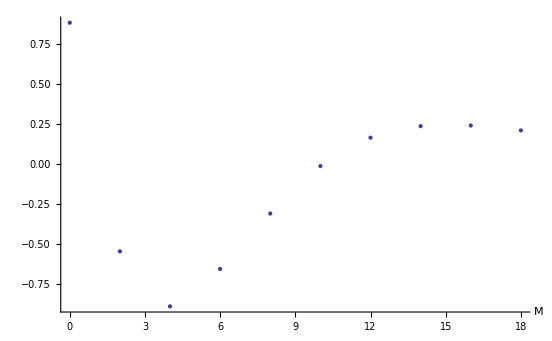

```mathematica
x=4.1
aaa=N[{{0,Amp0},{2,Amp2},{4,Amp4},{6,Amp6},{8,Amp8},{10,Amp10},{12,Amp12},{14,Amp14},{16,Amp16},{18,Amp18}}]
ListPlot[Re[aaa],PlotStyle->PointSize[Large],AxesLabel->{"M",}]
```

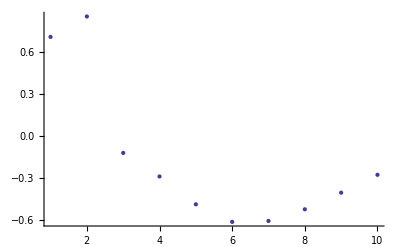

```mathematica
ListPlot[Re[aaa]]
```